Jacobians and Eigen analysis

```mathematica
Clear["Global`*"]
```

Disease impacts JUVENILE stage

```mathematica
(* Equations 4 *)
eqJS:=JS'[t]==f A[t]-(m0S-mbS*(JS[t]+JI[t]))*JS[t]-uJ JS[t]-betaJ JS[t]*JI[t];

eqJI:=JI'[t]==betaJ JS[t]*JI[t]-(m0I-mbI (JS[t]+JI[t]))*JI[t]-(uJ+alphaJ)*JI[t];

eqA:=A'[t]==(m0S-mbS (JS[t]+JI[t]))*JS[t]+(m0I-mbI (JS[t]+JI[t]))*JI[t]-uA A[t]; 

eqsol=FullSimplify[Solve[{eqJS[[2]]==0,eqJI[[2]]==0,eqA[[2]]==0},{JS[t],JI[t],A[t] }]];
eqsol[[1]]
eqsol[[2]]
eqsol[[3]];
eqsol[[4]];
(* Jacobian 4a: 4 because this figure was Figure 4a in an earlier version of the manuscript *)
Jac4a := ({{D[eqJS[[2]],JS[t]], D[eqJS[[2]],JI[t]], D[eqJS[[2]],A[t]]}, {D[eqJI[[2]],JS[t]], D[eqJI[[2]],JI[t]], D[eqJI[[2]],A[t]]}, {D[eqA[[2]],JS[t]], D[eqA[[2]],JI[t]], D[eqA[[2]],A[t]]}})
MatrixForm[Jac4a]
```

{JS[t]→0,JI[t]→0,A[t]→0}

{JS[t]→(f m0S-uA (m0S+uJ))/(mbS (f-uA)),JI[t]→0,A[t]→(f m0S uJ-uA uJ (m0S+uJ))/(mbS (f-uA)^2)}

(-m0S-uJ-betaJ JI[t]+mbS JS[t]+mbS (JI[t]+JS[t]) | -betaJ JS[t]+mbS JS[t] | f
betaJ JI[t]+mbI JI[t] | -alphaJ-m0I-uJ+mbI JI[t]+betaJ JS[t]+mbI (JI[t]+JS[t]) | 0
m0S-mbI JI[t]-mbS JS[t]-mbS (JI[t]+JS[t]) | m0I-mbI JI[t]-mbS JS[t]-mbI (JI[t]+JS[t]) | -uA)

Characteristic equation of Jacobian 4 evaluated for equilibrium in which J_I^* DOES NOT =0 (disease CAN persist).  Below lists polynomial coefficients starting with power 0.

```mathematica
Coeff2 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac4a/.eqsol[[2]],X],X]]
a0Eq2:=Coeff2[[1]]/Coeff2[[4]]
a1Eq2:=Coeff2[[2]]/Coeff2[[4]]
a2Eq2:=Coeff2[[3]]/Coeff2[[4]]
a3Eq2:=Coeff2[[4]]/Coeff2[[4]]

Coeff3 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac4a/.eqsol[[3]],X],X]]
a0Eq3:=Coeff3[[1]]/Coeff3[[4]]
a1Eq3:=Coeff3[[2]]/Coeff3[[4]]
a2Eq3:=Coeff3[[3]]/Coeff3[[4]]
a3Eq3:=Coeff3[[4]]/Coeff3[[4]]

Coeff4 :=Simplify[CoefficientList[CharacteristicPolynomial[Jac4a/.eqsol[[4]],X],X]]
a0Eq4:=Coeff4[[1]]/Coeff4[[4]]
a1Eq4:=Coeff4[[2]]/Coeff4[[4]]
a2Eq4:=Coeff4[[3]]/Coeff4[[4]]
a3Eq4:=Coeff4[[4]]/Coeff4[[4]]
RHEq2:=a0Eq2>0&&a2Eq2>0&&a2Eq2*a1Eq2-a0Eq2>0
RHEq3:=a0Eq3>0&&a2Eq3>0&&a2Eq3*a1Eq3-a0Eq3>0
RHEq4:=a0Eq4>0&&a2Eq4>0&&a2Eq4*a1Eq4-a0Eq4>0
```

For stability, the three following Routh-Hurwitz criterion must be satisfied:
i) a0 > 0
ii) a2 > 0
iii) a2a1 - a0 > 0

Persistence

Extinction (* No feasible interior equilibrium *)
(* Neither eqsol[[2]], eqsol[[3]], eqsol[[4]] are feasible, interior (i.e., at least one of each eq is ≤ 0) *)
NoDisease (* No interior equilibrium, edge equilibrium exists *)
Stable (* Not Extinction case && all R-H criteria are fulfilled *)
Unstable (* Not Extinction case && at least one of the R-H criteria are violated *)

```mathematica
(*feasibleEq2:=eqsol[[2]][[1]][[2]]>0&&eqsol[[2]][[3]][[2]]>0;
feasibleEq3:=eqsol[[3]][[1]][[2]]>0&&eqsol[[3]][[2]][[2]]>0&&eqsol[[3]][[3]][[2]]>0;
feasibleEq4:=eqsol[[4]][[1]][[2]]>0&&eqsol[[4]][[2]][[2]]>0&&eqsol[[4]][[3]][[2]]>0;
*)
feasibleEq2:=Element[eqsol[[2]][[1]][[2]],PositiveReals]&&Element[eqsol[[2]][[3]][[2]],PositiveReals];
(* IsIndetEq2:=(eqsol[[2]][[1]][[2]]===Indeterminate)||(eqsol[[2]][[2]][[2]]===Indeterminate)||(eqsol[[2]][[3]][[2]]===Indeterminate);
feasibleEq3:=Element[eqsol[[3]][[1]][[2]],PositiveReals]&&Element[eqsol[[3]][[2]][[2]],PositiveReals]&&Element[eqsol[[3]][[3]][[2]],PositiveReals]&&!(eqsol[[3]][[1]][[2]]===Indeterminate)&&!(eqsol[[3]][[2]][[2]]===Indeterminate)&&!(eqsol[[3]][[3]][[2]]===Indeterminate);
IsIndetEq3:=(eqsol[[3]][[1]][[2]]===Indeterminate)||(eqsol[[3]][[2]][[2]]===Indeterminate)||(eqsol[[3]][[3]][[2]]===Indeterminate);
feasibleEq4:=Element[eqsol[[4]][[1]][[2]],PositiveReals]&&Element[eqsol[[4]][[2]][[2]],PositiveReals]&&Element[eqsol[[4]][[3]][[2]],PositiveReals]&&!(eqsol[[4]][[1]][[2]]===Indeterminate)&&!(eqsol[[4]][[2]][[2]]===Indeterminate)&&!(eqsol[[4]][[3]][[2]]===Indeterminate);
IsIndetEq4:=(eqsol[[4]][[1]][[2]]===Indeterminate)||(eqsol[[4]][[2]][[2]]===Indeterminate)||(eqsol[[4]][[3]][[2]]===Indeterminate); *)
feasibleEq3:=Element[eqsol[[3]][[1]][[2]],PositiveReals]&&Element[eqsol[[3]][[2]][[2]],PositiveReals]&&Element[eqsol[[3]][[3]][[2]],PositiveReals];
IsIndetEq3:=(eqsol[[3]][[1]][[2]]===Indeterminate)||(eqsol[[3]][[2]][[2]]===Indeterminate)||(eqsol[[3]][[3]][[2]]===Indeterminate);
feasibleEq4:=Element[eqsol[[4]][[1]][[2]],PositiveReals]&&Element[eqsol[[4]][[2]][[2]],PositiveReals]&&Element[eqsol[[4]][[3]][[2]],PositiveReals];
IsIndetEq4:=(eqsol[[4]][[1]][[2]]===Indeterminate)||(eqsol[[4]][[2]][[2]]===Indeterminate)||(eqsol[[4]][[3]][[2]]===Indeterminate);

InteriorExists:=feasibleEq3||feasibleEq4;
Extinction1:=!feasibleEq2&&!feasibleEq3&&!feasibleEq4; (* No feasible interior equilibrium *)
Extinction:=!feasibleEq3&&!feasibleEq4; (* No feasible interior equilibrium *)(* Neither eqsol[[2]], eqsol[[3]], eqsol[[4]] are feasible, interior (i.e., at least one of each eq is ≤ 0) *)
ImEq2:=Im[eqsol[[2]][[1]][[2]]]==0&&Im[eqsol[[2]][[2]][[2]]]==0&&Im[eqsol[[2]][[3]][[2]]]==0
ImEq3:=Im[eqsol[[3]][[1]][[2]]]==0&&Im[eqsol[[3]][[2]][[2]]]==0&&Im[eqsol[[3]][[3]][[2]]]==0
ImEq4:=Im[eqsol[[4]][[1]][[2]]]==0&&Im[eqsol[[4]][[2]][[2]]]==0&&Im[eqsol[[4]][[3]][[2]]]==0

NoDisease:=!InteriorExists&&feasibleEq2
StableEq3:=feasibleEq3&&RHEq3; 
StableEq4:=feasibleEq4&&RHEq4; 
UnstableEq3:=feasibleEq3&&!RHEq3
UnstableEq4:=feasibleEq4&&!RHEq4
Stable := StableEq3||StableEq4; (* Interior exists and Dom Eig is stable *)
Unstable:=UnstableEq3||UnstableEq4;(* Interior exists and Dom Eig is not stable *)
DoubleCheck1:=UnstableEq3&&UnstableEq4
DoubleCheck2:=StableEq3&&StableEq4


(* results are different if individuals compete solely within a class; JS with JS only, JI with JI only *)
```

Figure 2A

Figure 2A

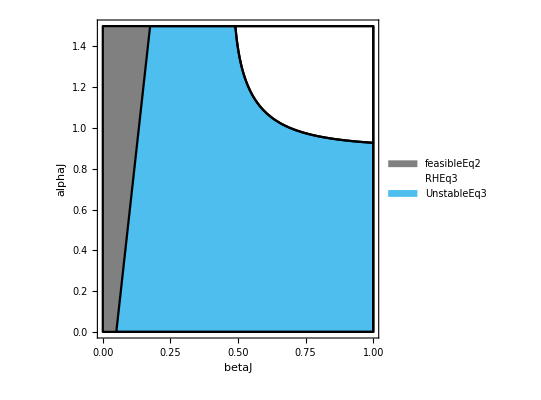

```mathematica
f=3;
uJ=0.5;
m0S=2.5;
alphaJ=0; 
uA=0.5;
mbS=0.2;
mbI=mbS;
m0I=2.5;

"Figure 2A"
RegionPlot[{feasibleEq2,RHEq3,UnstableEq3},{betaJ,0,1.0}, {alphaJ, 0, 3*uJ}, PlotLegends->"Expressions", FrameLabel-> Automatic,LabelStyle->Large,PlotStyle->{RGBColor[0.5, 0.5, 0.5], White, RGBColor[0.301, 0.745, 0.933]},BoundaryStyle->{Black}]
```